## codefour: 1D Burger's error analysis for analytic Hopf-Cole solution

## First hit "Browse..." and select an HDF5 input file from codefour. Then select all cells and evaluate them using Control-A followed by Shift-Enter.

```mathematica
{FileNameSetter[Dynamic[filename],"Open"], Dynamic[filename]}
```

{Browse…,}

## Parameters that fix the analytic solution:

```mathematica
A = 1; (* Magnitude *)
B = 1; (* Phase Shift *)
Const = 10/9; (* Constant offset *)
ν = 1/100; (* Diffusion coefficient *)
μ = 3; (* Frequency *)
u[x_, t_] := A Exp[-ν μ^2 t] Cos[μ x + B] + Const (* Heat *)
w[x_, t_] = -2 ν D[u[x, t], x]/u[x, t](* Hopf-Cole *);
```

## Closed form solution for the given parameters:

```mathematica
w[x,t]
```

(3 ⅇ^(-9 t/100) Sin[1+3 x])/(50 (10/9+ⅇ^(-9 t/100) Cos[1+3 x]))

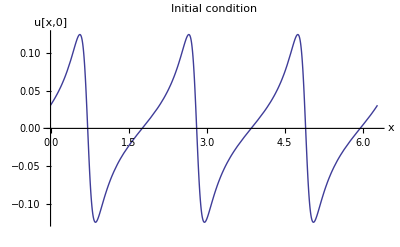

```mathematica
Plot[w[x,0],{x,0,2π},PlotRange->Full, PlotLabel->"Initial condition",AxesLabel->{"x","u[x,0]"}]
```

```mathematica
Plot3D[w[x, t], {x, 0, 2 π}, {t, 0, 1}, PlotRange -> Full,PlotLabel->"Full solution",AxesLabel->{"x","t","u[x,t]"}]
```

-Graphics3D-

## The discrete approximation loaded from HDF5:

```mathematica
{uh,xh,th}=Map[
(Import[filename,{"Datasets",#} ])&,{"/u","/x","/t"}];
range =DataRange->{{Min[xh],Max[xh]},{Min[th],Max[th]}};
```

```mathematica
ListPlot3D[uh,range,PlotRange->Full,PlotLabel->"Discrete Approximation", AxesLabel->{"x","t","u^h[x,t]"}]
```

-Graphics3D-

## Error present in the discrete approximation:

```mathematica
exact = Table[w[2π x,t],{t,th},{x,xh}];
error = exact - uh;
```

```mathematica
ListPlot3D[error,range,PlotRange->Full,PlotLabel->"Error evolution", AxesLabel->{"x","t","u-u^h"}]
```

-Graphics3D-

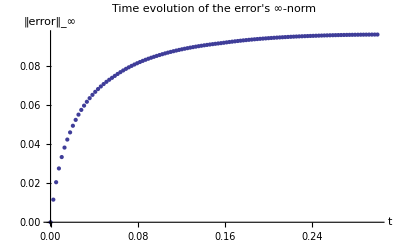

```mathematica
ListPlot[Max /@Abs[error],DataRange->{Min[th],Max[th]},PlotRange->Full,PlotLabel->"Time evolution of the error's ∞-norm",AxesLabel->{"t","‖error‖_∞"} ]
```

## Investigating the exact and discrete solutions at each time step:

```mathematica
Manipulate[ListPlot[{
exact[[i+1]],uh[[i+1]]
},PlotLabel->"Exact and Approximate Evolution",AxesLabel->{"x","u[x,t_i]"}],
{{i,0,"Time step index"}, 0,Dimensions[error][[1]],1}]
```